```mathematica
ClearAll["Global`*"]
```

```mathematica
outerProductLayer[vecDim1_,vecDim2_]:=NetGraph[{ReshapeLayer[{vecDim1,1}],ReshapeLayer[{1,vecDim2}],DotLayer[],FlattenLayer[]},{NetPort["Input1"]->1,NetPort["Input2"]->2,{1,2}->3->4}]
reshapeLayer[dimensions_,cuts_]:=ReshapeLayer[MovingMap[(Times@@dimensions[[#[[1]];;#[[2]]-1]])&,Join[{1},cuts,{0}],1]]
```

```mathematica
meraJoin[dimensions_]:=Module[{w0Dims=ConstantArray[dimensions[[1]],3]},
NetGraph[
<|
"input_1"->PartLayer[-1],
"input_2"->PartLayer[1],
"input_1_reshape"->reshapeLayer[dimensions,{-1}],
"input_2_reshape"->reshapeLayer[dimensions,{2}],
"w0_transpose"->TransposeLayer[1->2],
"w0_reshape"->reshapeLayer[w0Dims,{2}],
"dot_1"->DotLayer[],
"reshape"->reshapeLayer[dimensions[[;;-2]]~Join~w0Dims[[2;;]],{-1}],
"dot_2"->DotLayer[]
|>,
{NetPort["Input"]->"input_1"->"input_1_reshape",NetPort["Input"]->"input_2"->"input_2_reshape",NetPort["w0"]->"w0_transpose"->"w0_reshape",{"input_1_reshape","w0_reshape"}->"dot_1"->"reshape",{"reshape","input_2_reshape"}->"dot_2"}]
]

meraUWW[dimensions_]:=Module[{
cut=(Length@dimensions+1)/2+1,
rotatedDims=RotateLeft[dimensions,(Length@dimensions+1)/2],
uDims=ConstantArray[dimensions[[(Length@dimensions+1)/2-1]],2]~Join~ConstantArray[dimensions[[(Length@dimensions+1)/2]],2],
wDims=ConstantArray[dimensions[[(Length@dimensions+1)/2-1]],3]
},
NetGraph[
<|
"input_reshape_in"->reshapeLayer[dimensions,{cut-1}],
"input_transpose"->TransposeLayer[],
"input_reshape_out"->reshapeLayer[RotateRight[rotatedDims,1],{3}],
"u_reshape"->reshapeLayer[uDims,{3}],
"dot_u"->DotLayer[],
"reshape_1_in"->reshapeLayer[uDims[[;;2]]~Join~rotatedDims[[2;;-2]],{-1}],
"transpose_1"->TransposeLayer[],
"reshape_1_out"->reshapeLayer[RotateRight[uDims[[;;2]]~Join~rotatedDims[[2;;-2]],1],{3}],
"w_reshape"->reshapeLayer[wDims,{2}],
"dot_w_1"->DotLayer[],
"transpose_2"->TransposeLayer[],
"reshape_2_out"->reshapeLayer[uDims[[2;;2]]~Join~rotatedDims[[2;;-3]]~Join~wDims[[1;;1]],{3}],
"dot_w_2"->DotLayer[],
"reshape_3_in"->reshapeLayer[wDims[[1;;1]]~Join~rotatedDims[[3;;-3]]~Join~wDims[[1;;1]],{cut-2}],
"transpose_3"->TransposeLayer[]
|>,
{
"input_reshape_in"->"input_transpose"->"input_reshape_out",
{"u_reshape","input_reshape_out"}->"dot_u"->"reshape_1_in"->"transpose_1"->"reshape_1_out",
{"w_reshape","reshape_1_out"}->"dot_w_1"->"transpose_2"->"reshape_2_out",
{"w_reshape","reshape_2_out"}->"dot_w_2"->"reshape_3_in"->"transpose_3",
NetPort["u"]->"u_reshape",
NetPort["w"]->"w_reshape"
}]
]

meraU[dimensions_,meraNumber_]:=Module[{
cut=(Length@dimensions+1)/2+1,
rotatedDims=RotateLeft[dimensions,(Length@dimensions+1)/2],
uDims=ConstantArray[meraNumber,2]~Join~ConstantArray[dimensions[[(Length@dimensions+1)/2]],2]
},
NetGraph[
<|
"input_reshape_in"->reshapeLayer[dimensions,{cut-1}],
"input_transpose"->TransposeLayer[],
"input_reshape_out"->reshapeLayer[RotateRight[rotatedDims,1],{3}],
"u_reshape"->reshapeLayer[uDims,{3}],
"dot_u"->DotLayer[],
"reshape_3_in"->reshapeLayer[uDims[[;;2]]~Join~rotatedDims[[2;;-2]],{cut}],
"transpose_3"->TransposeLayer[]
|>,
{
"input_reshape_in"->"input_transpose"->"input_reshape_out",
{"u_reshape","input_reshape_out"}->"dot_u"->"reshape_3_in"->"transpose_3",
NetPort["u"]->"u_reshape"
}]
]

meraW[dimensions_]:=Module[{
cut=(Length@dimensions+1)/2+1,
rotatedDims=RotateLeft[dimensions,(Length@dimensions+1)/2],
wDims=ConstantArray[dimensions[[(Length@dimensions+1)/2+1]],3]
},
NetGraph[
<|
"input_reshape_in"->reshapeLayer[dimensions,{cut-2}],
"input_transpose"->TransposeLayer[],
"input_reshape_out"->reshapeLayer[RotateRight[rotatedDims,2],{3}],
"w_reshape"->reshapeLayer[wDims,{2}],
"dot_w_1"->DotLayer[],
"reshape_3_in"->reshapeLayer[wDims[[1;;1]]~Join~rotatedDims[[;;-3]],{cut}],
"transpose_3"->TransposeLayer[]
|>,
{
"input_reshape_in"->"input_transpose"->"input_reshape_out",
{"w_reshape","input_reshape_out"}->"dot_w_1"->"reshape_3_in"->"transpose_3",
NetPort["w"]->"w_reshape"
}]
]

meraShrink[dimensions_,meraNumber_]:=Module[{
netList={},
netRules,
dims=dimensions,
order=((Length@dimensions+1)/2-1)/2-1
},
Do[
netList~AppendTo~meraUWW[dims];
(*netList~AppendTo~ConstantArrayLayer["Array"->RandomReal[{-1.,1.},ConstantArray[dims[[(Length@dims+1)/2-1]],2]~Join~ConstantArray[dims[[(Length@dims+1)/2]],2]]];
netList~AppendTo~ConstantArrayLayer["Array"->RandomReal[{-1.,1.},ConstantArray[dims[[(Length@dims+1)/2-1]],3]]];*)
dims=dims[[;;(Length@dims+1)/2-1]]~Join~dims[[(Length@dims+1)/2+2;;]],
order];
netList~AppendTo~meraU[dims,meraNumber];
(*netList~AppendTo~ConstantArrayLayer["Array"->RandomReal[{-1.,1.},ConstantArray[meraNumber,2]~Join~ConstantArray[dims[[(Length@dims+1)/2]],2]]];*)

netRules=Flatten@Table[{
NetPort[i,"Output"]->NetPort[i+1,"Input"],
NetPort["u"<>ToString[i]]->NetPort[i,"u"],
NetPort["w"<>ToString[i]]->NetPort[i,"w"]
(*,
(3i-1)->NetPort[3i-2,"u"],
(3i)->NetPort[3i-2,"w"]*)
},{i,1,order}]~Join~{NetPort["u"<>ToString[order+1]]->NetPort[order+1,"u"]};
NetGraph[netList,netRules]
]

meraMap[dimensions_,meraNumber_,renormLags_]:=Module[{
order=(Length@dimensions+1)/2-1,
newDims=dimensions[[;;(Length@dimensions+1)/2]]~Join~{meraNumber,meraNumber}~Join~dimensions[[(Length@dimensions+1)/2+1;;]],
netList,netRules
},
netList=Table[
NetGraph[{
PartLayer[2i-1;;2i],
meraJoin[dimensions],
meraShrink[dimensions~Join~dimensions[[2;;]],meraNumber],
FlattenLayer[]
},{1->NetPort[2,"Input"],NetPort[2,"Output"]->NetPort[3,"Input"],NetPort[3,"Output"]->4}],
{i,1,renormLags/2}
]~Join~{CatenateLayer[],reshapeLayer[{renormLags/2}~Join~newDims,{2}]};
If[renormLags/2>1,
netRules={NetPort["Input"]->Table[NetPort[i,"Input"],{i,renormLags/2}],Table[NetPort[i,"Output"],{i,renormLags/2}]->renormLags/2+1->renormLags/2+2};,
netList=Delete[netList,-2];netRules={NetPort["Input"]->NetPort[1,"Input"],NetPort[1,"Output"]->renormLags/2+1}
];
NetGraph[netList,netRules]
]

meraMap0[dimension_,meraNumber_,lags_]:=Module[{netList,netRules},
netList=Table[
NetGraph[{
PartLayer[4i-3],PartLayer[4i-2],PartLayer[4i-1],PartLayer[4i],
NetChain[{TransposeLayer[3->2],TransposeLayer[2->1],ReshapeLayer[{dimension,meraNumber*meraNumber*dimension}]}],
DotLayer[],DotLayer[],
ReshapeLayer[{meraNumber*meraNumber,dimension}],ReshapeLayer[{meraNumber*meraNumber,dimension}],
DotLayer[],DotLayer[],
ReshapeLayer[{meraNumber,meraNumber}],ReshapeLayer[{meraNumber,meraNumber}],
NetChain[{TransposeLayer[1->2],ReshapeLayer[{meraNumber,meraNumber*meraNumber}]}],
DotLayer[],
ReshapeLayer[{meraNumber*meraNumber,meraNumber}],
DotLayer[],
FlattenLayer[]
},{
NetPort["u0"]->5,
{4,5}->6->8,{2,5}->7->9,
{8,3}->10->12,{9,1}->11->13,
NetPort["w0"]->14,
{12,14}->15->16,
{16,13}->17->18
}],
{i,1,lags/4}]~Join~{CatenateLayer[],ReshapeLayer[{lags/4,meraNumber*meraNumber*meraNumber}]};
If[lags/4>1,
netRules={NetPort["Input"]->Table[NetPort[i,"Input"],{i,lags/4}],Table[NetPort[i,"Output"],{i,lags/4}]->lags/4+1->lags/4+2},
netList=Delete[netList,-2];netRules={NetPort["Input"]->NetPort[1,"Input"],NetPort[1,"Output"]->lags/4+1}
];
NetGraph[netList,netRules]
]

meraFinish[dimensions_,hiddenVecDim_]:=Module[{
netList={},
netRules,
dims={1}~Join~dimensions[[(Length@dimensions+1)/2+1;;]]~Join~dimensions[[2;;(Length@dimensions+1)/2]],
cut=(Length@dimensions+1)/2+1,
order=(Length@dimensions+1)/2-2
},
netList~AppendTo~NetGraph[{reshapeLayer[dimensions,{cut}],TransposeLayer[],meraW[RotateLeft[dimensions,cut-1]]},{1->2->NetPort[3,"Input"]}];
Do[
netList~AppendTo~meraUWW[dims];
dims=dims[[;;(Length@dims+1)/2-1]]~Join~dims[[(Length@dims+1)/2+2;;]];,
order];
netList~AppendTo~NetChain[{(*ReshapeLayer[{1,dims[[-2]],dims[[-1]]}],ConvolutionLayer[1,{Floor[dims[[-2]]/2],Floor[dims[[-1]]/2]}],ElementwiseLayer[Tanh],*)LinearLayer[hiddenVecDim]}];
netRules={NetPort["w0"]->NetPort[1,"w"]}~Join~Flatten[Table[{
NetPort[i,"Output"]->NetPort[i+1,"Input"],
NetPort["u"<>ToString[i]]->NetPort[i+1,"u"],
NetPort["w"<>ToString[i]]->NetPort[i+1,"w"]
},{i,1,order}]]~Join~{NetPort[order+1,"Output"]->NetPort[order+2,"Input"]};
NetGraph[netList,netRules]
]

mera[inputSteps_,inputVecDim_,meraNumbers_,hiddenVecDim_]:=Module[{
netList={meraMap0[inputVecDim,meraNumbers[[1]],inputSteps]},netRules,order=Length@meraNumbers-1,dims=ConstantArray[meraNumbers[[1]],3],g,a=meraNumbers~Prepend~inputVecDim
},
Do[
netList~AppendTo~meraMap[dims,meraNumbers[[i+1]],inputSteps/2^(i+1)];
dims=dims[[;;i+1]]~Join~{meraNumbers[[i+1]],meraNumbers[[i+1]]}~Join~dims[[-i;;]];
,
{i,order}];
netList~AppendTo~meraFinish[dims,hiddenVecDim];
netRules=Table[NetPort[i,"Output"]->NetPort[i+1,"Input"],{i,order+1}];
g=NetGraph[netList,netRules];
netList={g}~Join~Flatten@Table[{ConstantArrayLayer["Array"->RandomReal[{-1,1},{a[[i+1]],a[[i+1]],a[[i]],a[[i]]}]],ConstantArrayLayer["Array"->RandomReal[{-1,1},{a[[i+1]],a[[i+1]],a[[i+1]]}]]},{i,order+1}];
netRules=Flatten@Table[{(2i)->NetPort[1,"u"<>ToString[i-1]],(2i+1)->NetPort[1,"w"<>ToString[i-1]]},{i,1,order+1}];
NetGraph[netList,netRules]
]
```

```mathematica
meraNumbers={2,2,2};
inputSteps=2^(Length[meraNumbers]+1);
inputVecDim=1;
polyOrder=2;
hiddenVecDim=2;
outputSteps=1;
```

```mathematica
(*Subscript[x, t]=4 Subscript[x, t-1](Subscript[x, t-1]-1)*)
rawData=Transpose[{NestList[4#(1-#)&,0.1,1000]}];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+outputSteps,1]];
rawData=Transpose[{NestList[4#(1-#)&,0.32,100]}];
testData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+outputSteps,1]];
```

```mathematica
(*Subscript[x, t]=16 Subscript[x, -1+t]-80 Subscript[x, -1+t]^2+128 Subscript[x, -1+t]^3-64 Subscript[x, -1+t]^4*)
(*CONCLUSION:it will converge by adding a perturbation and a repulsive force!*)
rawData=Transpose[{NestList[16#-80#^2+128#^3-64#^4&,0.31,1000]}];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+outputSteps,1]];
rawData=Transpose[{NestList[16#-80#^2+128#^3-64#^4&,0.11,100]}];
testData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+outputSteps,1]];
```

```mathematica
(*Psudo-Random.*)
SeedRandom[1,Method->"Congruential"];
rawData=Transpose@{RandomReal[1,2100]};
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData[[;;2000]],inputSteps+outputSteps,1]];
rawData=rawData;
testData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData[[2001;;]],inputSteps+outputSteps,1]];
```

```mathematica
meraCone=NetInitialize[NetChain[{
NetGraph[Table[ElementwiseLayer[(*Tanh@*)LegendreP[i+1,#]&],{i,polyOrder-1}]~Join~{CatenateLayer[2]},{{NetPort["Input"]}~Join~Range[polyOrder-1]->polyOrder}],
PaddingLayer[{{0,0},{1,0}},"Padding"->1,"Input"->{inputSteps,inputVecDim*polyOrder}],
mera[inputSteps,inputVecDim*polyOrder+1,meraNumbers,hiddenVecDim],
ElementwiseLayer[Tanh],
LinearLayer[inputVecDim]
},"Input"->{inputSteps,inputVecDim}]];
```

```mathematica
meraCone=NetTrain[meraCone,trainingData,ValidationSet->Scaled[0.05],(*TargetDevice->"GPU",*)Method->{"ADAM","LearningRate"->0.01,"L2Regularization"->10^-5}];
```

```mathematica
meraConeStretched=
NetGraph[
<|
"shake"->NetGraph[{PartLayer[;;-2],PartLayer[-1;;-1],ElementwiseLayer[Ramp[#-0.001]&],CatenateLayer[]},{NetPort["Input"]->{1,2},2->3,{1,3}->4},"Input"->{inputSteps,inputVecDim}],
"reshape_in_1"->ReshapeLayer[{1,inputSteps,inputVecDim}],
"reshape_in_2"->ReshapeLayer[{1,inputSteps,inputVecDim}],
"catenate"->CatenateLayer[],
"meraCone"->NetMapOperator[meraCone],
"reshape_out"->ReshapeLayer[{2*inputVecDim}],
"part_1"->PartLayer[;;inputVecDim],
"part_2"->PartLayer[inputVecDim+1;;],
"loss"->MeanSquaredLossLayer[],
"stretch"->NetGraph[{ThreadingLayer[(Abs[#1-#2]-0.001)^2/0.001^2&],AggregationLayer[Mean,1;;All]},{{NetPort["1"],NetPort["2"]}->1->2}(*,"Input"->{inputVecDim}*)],
"loss+strentch"->ThreadingLayer[(#1+5.#2)&]
|>,
{NetPort["Input"]->"reshape_in_1",NetPort["Input"]->"shake"->"reshape_in_2",{"reshape_in_1","reshape_in_2"}->"catenate"->"meraCone"->"reshape_out","reshape_out"->"part_1"->NetPort["Output"],"part_1"->NetPort["loss","Input"],"part_1"->NetPort["stretch","1"],"reshape_out"->"part_2"->NetPort["stretch","2"],{"loss","stretch"}->"loss+strentch"->NetPort["Loss"]}
];
meraConeStretched=NetTrain[meraConeStretched,trainingData,ValidationSet->Scaled[0.05],TargetDevice->"GPU",Method->{"ADAM","LearningRate"->0.01,"L2Regularization"->10^-5}];
meraCone=meraConeStretched[["meraCone","Net"]];
```

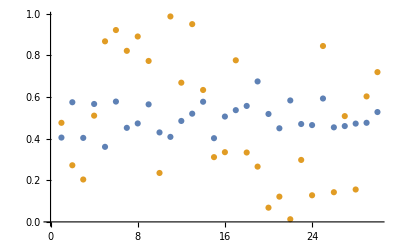

```mathematica
ListPlot[Transpose[meraCone/@testData[[;;30,1]]]~Join~Transpose[testData[[;;30,2]]]]
```

```mathematica
Mean[Flatten[0.5-testData[[;;,2]]]^2]
Mean[Flatten[meraCone/@testData[[;;,1]]-testData[[;;,2]]]^2]
```

0.0860057

0.0890559

```mathematica
meraFinish[{3,3,2,4,7,7,4,2,3},5]
```

NetGraph[]

```mathematica
{3,2,4,7}
```

```mathematica
mera[32,5,{3,2,3,4},5]
```

NetGraph[]

```mathematica
tmp=NetGraph[{meraMap0[5,3,32],meraMap[{3,3,3},2,8],meraMap[{3,3,2,2,3},4,4],meraMap[{3,3,2,4,4,2,3},7,2],meraFinish[{3,3,2,4,7,7,4,2,3},5]},{1->2->3->4->NetPort[5,"Input"]}]
(* Output dims: {1,7,7} *)
```

NetGraph[]

```mathematica
cool=NetInitialize@NetGraph[{tmp}~Join~{ConstantArrayLayer["Array"->RandomReal[{-1,1},{3,3,5,5}]],ConstantArrayLayer["Array"->RandomReal[{-1,1},{3,3,3}]],ConstantArrayLayer["Array"->RandomReal[{-1,1},{2,2,3,3}]],ConstantArrayLayer["Array"->RandomReal[{-1,1},{2,2,2}]],ConstantArrayLayer["Array"->RandomReal[{-1,1},{4,4,2,2}]],ConstantArrayLayer["Array"->RandomReal[{-1,1},{4,4,4}]],ConstantArrayLayer["Array"->RandomReal[{-1,1},{7,7,4,4}]],ConstantArrayLayer["Array"->RandomReal[{-1,1},{7,7,7}]]},Flatten@Table[{(2i)->NetPort[1,"u"<>ToString[i-1]],(2i+1)->NetPort[1,"w"<>ToString[i-1]]},{i,1,4}],"Input"->{32,5}]
```

NetGraph[]

```mathematica
cool@RandomReal[{-1,1},{32,5}]
```

{4.03873×10^10,3.6841×10^10,2.03703×10^10,9.68146×10^9,-1.00716×10^10}

```mathematica
meraJoin[{3,3}]
```

NetGraph[]

```mathematica
meraUW[{3,3,2,4,4,2,3,3,2,4,4,2,3}]
meraNew[{3,3,2,4,4,2,3,3,2,4,4,2,3},7]
```

NetGraph[]

NetGraph[]

```mathematica
meraShrink[{3,3,2,4,4,2,3,3,2,4,4,2,3},7]
```

NetGraph[]